# Ultra High Vacuum Calculations

#### Referencess

OHanlon is a big one

#### Constants

Input important fundamental constants. We also keep track of the average thermal speed v which comes up often in conductance calculations

```mathematica
kB=1.380649×10^-23;
amu = 1.6605 10^-27;
mH2 = 2 amu;
mH20;
m=mH2;
T = 22 + 273.15; 
v = √((8 kB T)/(π m))
```

1767.66

#### Import Numerical Simulations

```mathematica
SetDirectory[NotebookDirectory[]]


Import["round_pipe.h5",{"HDF5","Datasets"}]
roundpipeL=Flatten@Import["round_pipe.h5",{"HDF5","/L"}];
roundpipeT=Flatten@Import["round_pipe.h5",{"HDF5","/T"}];
roundpipesigmaT=Flatten@Import["round_pipe.h5",{"HDF5","/sigmaT"}];
roundpipeNattempt=Flatten@Import["round_pipe.h5",{"HDF5","/Nattempt"}];
roundpipeNtransmit=Flatten@Import["round_pipe.h5",{"HDF5","/Ntransmit"}];
roundpipe=Transpose[{roundpipeL,roundpipeT}];
```

C:\Users\coraf\GitHub\Vacuum-Calculations

{/metadata/description,/sigmaT,/T,/Nattempt,/L,/Ntransmit}

## Conductance of 2.75” Flange

Many pumping elements are limited by a 2.75” OD flange, which also has a corresponding inner diameter

```mathematica
Clear[L,R,d,Corifice,Cnipple,Cdpt]
L=4.9 0.0254; (*Typical flange Length in m*)
R = 1.5/2 0.0254; (*Typical flange inner radius in m*)
d = 2R; (*Typical flange inner diameter in m*)
LoverR = 100;
```

```mathematica
Corifice[r_]:= 1/4(π r^2)v; (* in m^3/s*) 
Cnipple[r_,L_]:= Corifice[r] 4/3(2r)/L;(* in m^3/s*)
Cdpt[r_,L_]:= Corifice [r] 4/3(2r)/L;
```

```mathematica
10^3 Corifice[R]
10^3 Cnipple[R,L]
10^3 Cdpt[L/LoverR,L]
```

503.696

205.59

0.0573332

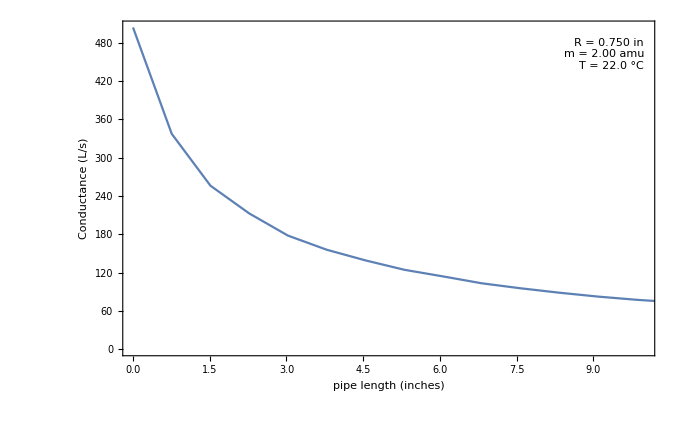

```mathematica
paramText=Column[{Row[{"R = ",NumberForm[R/0.0254,{4,3}]," in"}],Row[{"m = ",NumberForm[m/amu,{4,2}]," amu"}],Row[{"T = ",NumberForm[T-273.15,{4,1}]," °C"}]},Alignment->Right];
p2=ListPlot[Transpose[{roundpipeL R/0.0254,roundpipeT 10^3 Corifice[R]}],Joined->True,PlotRange->{{0,10},All},Frame->True,FrameLabel->{"pipe length (inches)","Conductance (L/s)"},Epilog->{Inset[Framed[Style[paramText,14],Background->White,FrameStyle->None,RoundingRadius->5,FrameMargins->Medium],Scaled[{0.98,0.95}],{Right,Top}]}]
```